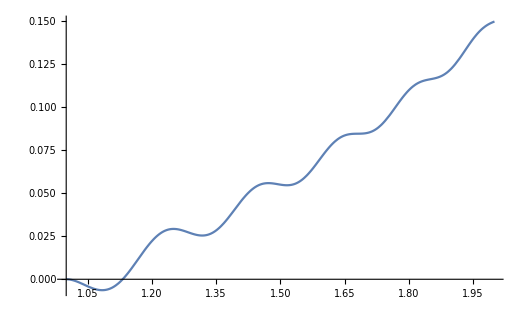

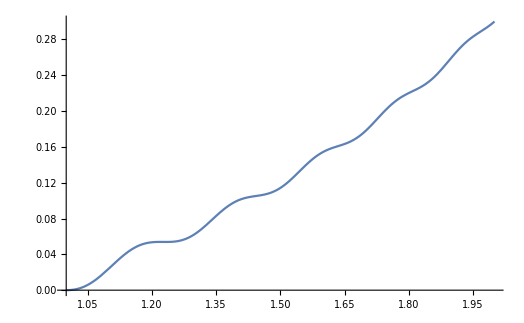

```mathematica
n =3;
GAMMA = 1;
Q =1;
s = 20*I;
Plot[Re[Integrate[E^(-(n*I*Log[zita]*GAMMA/Q+s*zita^2/2/Q))*(r^n*zita^(-n+1)-r^(-n)*zita^(n+1)),{zita,1,r}]],{r,1.0,2.0}]
Plot[Im[Integrate[E^(-(n*I*Log[zita]*GAMMA/Q+s*zita^2/2/Q))*(r^n*zita^(-n+1)-r^(-n)*zita^(n+1)),{zita,1,r}]],{r,1.0,2.0}]
```

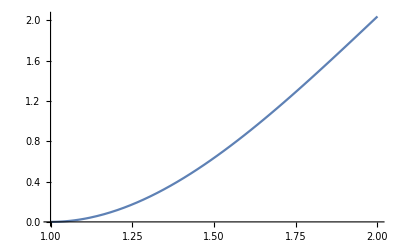

ConditionalExpression[1/170 (((-102+306 ⅈ) r^(4-3 ⅈ)+(102-306 ⅈ) r^5)/r^3-(3 ((25+15 ⅈ)-(42-36 ⅈ) r^(5-3 ⅈ)+(17-51 ⅈ) r^6))/r^4) Re'[((25+15 ⅈ)-(42-36 ⅈ) r^(5-3 ⅈ)+(17-51 ⅈ) r^6)/r^3], Re[r]>0||r∉ℝ]

```mathematica
n =3;
GAMMA = 1;
Q =1;
s = 0;
f[r_] = Re[Integrate[E^(-(n*I*Log[zita]*GAMMA/Q+s*zita^2/2/Q))*(r^n*zita^(-n+1)-r^(-n)*zita^(n+1)),{zita,1,r}]];
Plot[f[r],{r,1.0,2.0}]
df[r_]=D[f[r],r]
```